```mathematica
14.5 a
```

14.5 a

```mathematica
y[x_,t_]= (12 k^2 α)/(Cosh[k(x-x0-4α k^2 t)]^2);
x0=L/2;
D[y[x,t],t] + y [x,t]* D[y[x,t],x] + α D[y[x,t],{x,3}]//FullSimplify
```

0

```mathematica
y0 = y[x,0]//FullSimplify
```

12 k^2 α Sech[k (-L/2+x)]^2

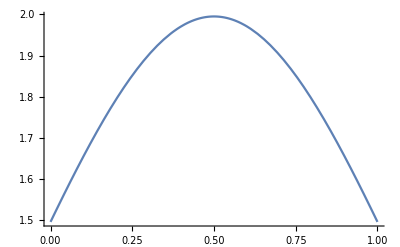

```mathematica
Plot[y0/.{k->1.1, α->.1374, L->1}, {x,0,1}]
```